# UniDyn--Demo-Scratch.nb

John A. Marohn
jam99@cornell.edu
Cornell University

Abstract:  This demonstration notebook loads the UniDyn package and executes the package’s unit tests.

## Set the path to the package

Tell Mathematica the path to the directory containing the package.    

EDIT THE FOLLOWING PATH STRING:

```mathematica
$PackagePath ="/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn";
```

YOU SHOULD NOT NEED TO EDIT ANYTHING FROM HERE ONWARDS.

## Load the package

Append the package path to the system path.  Before trying to load the package, ask Mathematica to find it.  This is a test that we directed Mathematica to the correct directory.  The output of this command should be the full system path to the UniDyn.m file.

```mathematica
$Path = AppendTo[$Path,$PackagePath];
FindFile["UniDyn`"]
```

/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/UniDyn/UniDyn.m

Now that we are confident that the path is set correctlly, load the package.  Setting the global $VerboseLoad variable to True will print out the help strings for key commands in the package.

```mathematica
$VerboseLoad =True;
Needs["UniDyn`"]
```

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

NCMultiplication.m loaded

NC1SetCommands.m loaded

NCInverses.m loaded

NCTransposes.m loaded

NCAdjoints.m loaded

NCCo.m loaded

NCRoots.m loaded

NC2SetCommands.m loaded

NCCollect.m loaded

NCSubstitute.m loaded

NCMonomial.m loaded

NCSolve.m loaded

NCTools.m loaded

NC2SimplifyRational.m loaded

NC1SimplifyRational.m loaded

NCSimplifyRational.m loaded

NCComplex.m loaded

NCMatMult.m loaded

NCDiff.m loaded

NCSchur.m loaded

NCAlias.m loaded

Grabs.m loaded

NCTaylorCoeff.m loaded

NCConvexity.m and NCGuts.m loaded

NCRealizationFunctions.m loaded

NCTeXForm.m loaded

NCTeX::Using 'open' as PDFViewer.

NCTeX.m loaded

NCMaster.m loaded

NCOutput.m loaded

------------------------------------------------------------
NCAlgebra - Version 4.0.6
Compatible with Mathematica Version 9

Authors:
  J. William Helton*
  Mauricio de Oliveira* 
  Mark Stankus* 
  Robert L. Miller#

* Math Dept, UCSD                
# General Atomics Corp
  La  Jolla, CA 92093

Copyright: 
  Helton and Miller June 1991
  Helton 2002
  All rights reserved.

The program was written by the authors and by:
  David Hurst, Daniel Lamm, Orlando Merino, Robert Obar,
  Henry Pfister, Mike Walker, John Wavrik, Lois Yu,
  J. Camino, J. Griffin, J. Ovall, T. Shaheen, John Shopple. 
  The beginnings of the program come from eran@slac.
  Considerable recent help came from Igor Klep.


This program was written with support from 
  AFOSR, NSF, ONR, Lab for Math and Statistics at UCSD,
  UCSD Faculty Mentor Program,
  and US Department of Education.
  Primary support in 2010 is from the 
    NSF Division of Mathematical Sciences.

If you 
  (1) are a user, 
  (2) want to be a user, 
  (3) refer to NCAlgebra in a publication, or 
  (4) have had an interesting experience with NCAlgebra,
let us know by sending an e-mail message to  

  ncalg@math.ucsd.edu. 

We do not want to restrict access to NCAlgebra, but do 
  want to keep track of how it is being used.

For NCAlgebra updates see the web page:

  www.math.ucsd.edu/~ncalg 
------------------------------------------------------------

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

CreateOperator::usage: CreateOperator[] is used to batch-define a bunch of operators. Example: CreateOperator[{{Ix, Iy, Iz},{Sx,Sy,Sz}}] will create six operators;  each of the operators in the first list is meant to commute with each of the operators in the second list.

CreateScalar::usage: CreateScalar[list] is used to batch-define a bunch of scalars. The parameter list can be a single scalar or a list of scalars.  Example: CreateScalar[{w1,w2}].

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

NCSort::usage: NCSort[list] sorts the operators in list into canonical order.

SortedMult::usage: SortedMult[list] returns Mult[list$ordered], where list$ordered are the elements of list sorted into canonical order.

MultSort::usage: MultSort[NonCommutativeMultiplyt[list]] returns returns NonCommutativeMultiply[list$ordered], where list$ordered are the elements of list sorted into canonical order.

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

Comm::usage: Comm[a,b] calculates the commutator of two operators.

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

SpinSingle$CreateOperators::usage: SpinSingle$CreateOperators[Ix,Iy,Iz,L] creates Ix, Iy, and Iz angular momentum operators and defines their commutation relations.  When the total angular momentum L = 1/2, additional rules are defined to simplify products of the angular momentum operators.  When the total angular momentum L is unspecified, no such simplification rules are defined.

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

OscSingle$CreateOperators::usage: OscSingle$CreateOperators[aL,aR] creates a raising operator aR and a lowering operator aL for single harmonic oscillator and defines the operator commutation relations.

You are using the version of NCAlgebra which is found in:

/Users/jam99/Downloads/NC

You can now use "<< NCAlgebra`" to load NCAlgebra or "<< NCGB`" to load NCGB.

You have already loaded NCAlgebra.m

Evolve::usage: Evolve[H,t,ρ] represents unitary evolution of the density operator ρ for a time t under the Hamiltonian H.  This function expands according to simplification rules but leaves the evolution unevaluated.

Evolver::usage: Evolver[H,t,ρ(0)] calculates ρ(t) = Exp[-I H t] ρ(0) Exp[+I H t], assuming that H is time independent, according to the commutation rules followed by ρ(0) and H.

## Execute the units tests in batch

Included with the package are a number of files, ending in “-tests.m”, that contain tests of the package’s functions -- so-called unit tests.  Set the working directory to the package directory and pretty-print the directory name.

```mathematica
SetDirectory[$PackagePath];
TableForm[{{$PackagePath}},TableHeadings->{None,{"Directory"}}]
```

Directory
/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn

Get the names of all the unit-testing files included with the package (following my convention that the unit testing file end in “-tests.m”).   Pretty-print the names of the unit-test files included with the package.

```mathematica
fn = FileNames["*-tests.m"];
TableForm[{{fn}},TableHeadings->{None,{"Test files found"}}]
```

Test files found
Comm-tests.m
Evolve-tests.m
Mult-tests.m
OpCreate-tests.m
Osc-tests.m
Spins-tests.m

Finally, carry out the unit tests and make a report.

```mathematica
tr =TestReport /@ fn;
TableForm[Table[tr [[k]],{k,1,Length[tr]}]]

tests$run$total = Plus @@ (tr[[#]]["TestsSucceededCount"]& /@ List @@ Table[k,{k,1,Length[tr]}]);
Print[Style["Total test run = " <> ToString[tests$run$total ],FontWeight-> Bold,FontSize-> 18,FontColor-> Blue]]
```

TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]
TestReportObject[…]

Total test run = 102

## Single spin: Taking repeated commutators

Create a  single-spin system to play with.

```mathematica
Needs["UniDyn`"];
Clear[H,Ix, Iy, Iz,Δ,ω]
CreateScalar[{Δ,ω}];
SpinSingle$CreateOperators[Ix, Iy, Iz];
```

SpinSingle$CreateOperators::create: Creating spin operators.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::nosimplify: No angular momentum L defined.

Define a Hamiltonian

```mathematica
H = Δ Iz + ω Ix;
```

### Repeated commutators

Define a function to take n commutators of an operator Op with the -i times the Hamiltonian H.

```mathematica
Clear[RepeatedComm];
RepeatedComm[1,H_,Op_] :=  List[Op];
RepeatedComm[n_,H_,Op_] :=  Prepend[RepeatedComm[n-1,H,Op],-I Comm[H,RepeatedComm[n-1,H,Op][[1]]]];
```

Example calculation of repeated commutators

```mathematica
σ = RepeatedComm[5,H,Iz] // Expand // Simplify;
σ // MatrixForm
```

(ω (-Ix Δ+Iz ω) (Δ^2+ω^2)
Iy ω (Δ^2+ω^2)
ω (Ix Δ-Iz ω)
-Iy ω
Iz)

### Evolution

Use the Evolver function to calculate the evolution of the I_x operator under the off-resonance Zeeman Hamiltonian.

```mathematica
$Assumptions = {Δ ∈Reals,Δ > 0, ω ∈Reals, ω>= 0};
ρ=Collect[Expand[Simplify[ExpToTrig[Evolver[H,t,Ix]]]],{Ix,Iy,Iz},Simplify]
```

(Ix (ω^2+Δ^2 Cos[t √(Δ^2+ω^2)]))/(Δ^2+ω^2)+(2 Iz Δ ω Sin[1/2 t √(Δ^2+ω^2)]^2)/(Δ^2+ω^2)+(Iy Δ Sin[t √(Δ^2+ω^2)])/(√(Δ^2+ω^2))

## Quantum optics

### Operators

```mathematica
Needs["UniDyn`"];
Clear[H,Ix, Iy, Iz,Δ,ω, g, F, aL,aR,Q$sym, P$sym, Q,P,QP$rules]
CreateScalar[{Δ,ω,Δω,g, F,ϕ}];
CreateOperator[{{Ix, Iy, Iz},{aL,aR}}];
SpinSingle$CreateOperators[Ix, Iy, Iz, 1/2];
OscSingle$CreateOperators[aL,aR];

Q$sym=(aR+aL)/Sqrt[2];
P$sym =I (aR-aL)/Sqrt[2];
QP$rules = {aR -> (Q + I P)/Sqrt[2], aL -> (Q - I P)/Sqrt[2]};
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

OscSingle$CreateOperators::nocreate: Oscillator operators already exist.

OscSingle$CreateOperators::comm: Adding oscillator commutations relations.

### Hamiltonians

#### Free evolution

```mathematica
$Assumptions = {Element[ω, Reals], ω > 0};
H$0 = ω/2 (aR**aL + aL**aR);
```

```mathematica
Simplify[Evolver[H$0,t,Q$sym]  /. QP$rules]
```

Q Cos[t ω]+P Sin[t ω]

#### Phase Kick

```mathematica
$Assumptions = {Element[ω, Reals], ω > 0};
H$0$kick = (ω+Δω)/2 (aR**aL + aL**aR) ;
```

```mathematica
Simplify[Evolver[H$0$kick,t,Q$sym]  /. QP$rules] /. {Δω-> Δϕ/t} // Simplify
```

Q Cos[Δϕ+t ω]+P Sin[Δϕ+t ω]

#### Force

```mathematica
$Assumptions = {Element[F, Reals], F > 0};
H$1 = F aL ;
```

```mathematica
Simplify[Evolver[H$1,t,aR]  /. QP$rules]
```

(ⅈ P+Q)/(√2)-ⅈ F t

#### Squeezing

```mathematica
$Assumptions = {Element[Δ, Reals], Δ > 0, Element[ω, Reals], ω > 0};
```

```mathematica
Simplify[Evolver[-Δ/2 I (aR**aR - aL**aL),t,#]  /. QP$rules]& /@ {Q$sym, P$sym}
```

{ⅇ^(t Δ) Q,-ⅇ^(-t Δ) P}

```mathematica
Simplify[Evolver[Δ/2 I (aR**aR - aL**aL),t,#]  /. QP$rules]& /@ {Q$sym, P$sym}
```

{ⅇ^(-t Δ) Q,-ⅇ^(t Δ) P}

```mathematica
Expand[Simplify[ExpToTrig[Evolver[Δ/2 (aR**aR + aL**aL),t,#]  /. QP$rules]]]& /@ {Q$sym, P$sym}
```

{Q Cosh[t Δ]-P Sinh[t Δ],-P Cosh[t Δ]+Q Sinh[t Δ]}

Let's remind ourselves what the hyperbolic functions look like

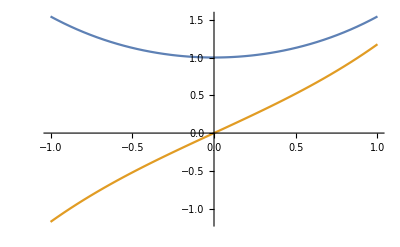

```mathematica
Plot[{Cosh[T],Sinh[T]},{T,-1,1}]
```

```mathematica
Collect[Simplify[ExpToTrig[Evolver[ ω/2 (aR**aL + aL**aR)-Δ/2 I (aR**aR - aL**aL),t,#]  /. QP$rules]],{Q,P}]& /@ {Q$sym, P$sym}
```

{(P ω Sinh[t √(Δ^2-ω^2)])/(√(Δ^2-ω^2))+(Q (√(Δ^2-ω^2) Cosh[t √(Δ^2-ω^2)]+Δ Sinh[t √(Δ^2-ω^2)]))/(√(Δ^2-ω^2)),(Q ω Sinh[t √(Δ^2-ω^2)])/(√(Δ^2-ω^2))+(P (-√(Δ^2-ω^2) Cosh[t √(Δ^2-ω^2)]+Δ Sinh[t √(Δ^2-ω^2)]))/(√(Δ^2-ω^2))}

## Failing cases

#### Off-resonance evolution of Iz is touchy

This Evolution broke in upgrading from Mathematica 10 to 11.  Figure out why.

```mathematica
Clear[Ix$sym, Iy$sym, Iz$sym, Sx$sym, Sy$sym, Sz$sym, ω, d$sym, Δ, rho$sym, t$sym]
Clear[A, r, lhs$list, rhs$list, time, eqns, system, rho$calc, rho$known, X]

CreateScalar[ω, d$sym, Δ];
CreateOperator[{{Ix$sym, Iy$sym, Iz$sym},{Sx$sym, Sy$sym, Sz$sym}}]

SpinSingle$CreateOperators[Ix$sym, Iy$sym, Iz$sym, L=1/2];
SpinSingle$CreateOperators[Sx$sym, Sy$sym, Sz$sym, L=1/2];
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

```mathematica
rho$known = Collect[
  constant1 Iz$sym + constant2 Ix$sym + (constant3 Iz$sym - constant2 Ix$sym) Cos[omega$eff t$sym] - constant4 Iy$sym Sin[omega$eff t$sym] // 
    Expand, {Ix$sym, Iy$sym, Iz$sym}];

rho$calc = Collect[
  Evolver[Δ Iz$sym + ω Ix$sym , t$sym, Iz$sym, quiet -> True] // FullSimplify, {Ix$sym, Iy$sym, Iz$sym},Expand];
```

```mathematica
rho$known
```

Ix$sym ((Δ ω)/(Δ^2+ω^2)-(Δ ω Cos[t$sym √(Δ^2+ω^2)])/(Δ^2+ω^2))+Iz$sym (Δ^2/(Δ^2+ω^2)+(ω^2 Cos[t$sym √(Δ^2+ω^2)])/(Δ^2+ω^2))-(Iy$sym ω Sin[t$sym √(Δ^2+ω^2)])/(√(Δ^2+ω^2))

```mathematica
rho$calc
```

Ix$sym ((Δ ω)/(Δ^2+ω^2)-(Δ ω Cos[t$sym √(Δ^2+ω^2)])/(Δ^2+ω^2))+Iz$sym (Δ^2/(Δ^2+ω^2)+(ω^2 Cos[t$sym √(Δ^2+ω^2)])/(Δ^2+ω^2))-(Iy$sym ω Sin[t$sym √(Δ^2+ω^2)])/(√(Δ^2+ω^2))

#### Force with a phase factor

```mathematica
$Assumptions = {Element[F, Reals], F > 0};
H$1 = F (Exp[-i ϕ] aL + Exp[i ϕ] aL );
```

```mathematica
Evolver[H$1,t,aR]
```

Evolver::unsolvable: Unrecognized evolution

{aR,-ⅈ F (Comm[aL ⅇ^(-i ϕ),aR]+Comm[aL ⅇ^(i ϕ),aR]),-F^2 (Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),aR]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),aR]]),ⅈ F^3 (Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]),F^4 (Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]]+Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(-i ϕ),aR]]]]+Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),Comm[aL ⅇ^(i ϕ),aR]]]])}